```mathematica
求导数：
```

```mathematica
k[x] = x +1;
Dt[k[x],x]

1
```

```mathematica
HTest[Aa_,Ab_,Ac_,ua_,ub_,uc_]:=D[]
```

```mathematica
1/0
```

Power::infy: 碰到无穷表达式 1/0.

ComplexInfinity

```mathematica
Manipulate[Column[{n,n^2,n^3}],{n,1,10,1}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Hue[h]]],{n,5,20,1},{h,0,1}]
```

```mathematica
Manipulate[Range[n],{n,0,100,1}]
```

```mathematica
Grid[Table[A[i,j],{i,3},{j,3}]]
```

A[1,1] | A[1,2] | A[1,3]
A[2,1] | A[2,2] | A[2,3]
A[3,1] | A[3,2] | A[3,3]



```mathematica
LinguisticAssistant["Flag"]
```

```mathematica
LinguisticAssistant["Population"]
```

1439323774 people

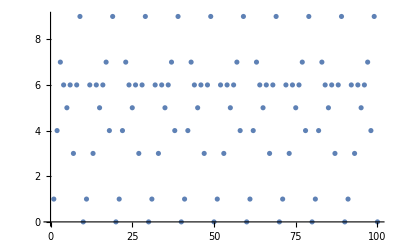

```mathematica
ListPlot[Table[Mod[n^n,10],{n,1,100,1}]]
```

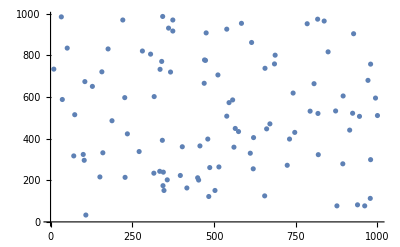

```mathematica
ListPlot[Table[RandomInteger[1000],100,2]]
```

```mathematica
f[#]&/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
f/@{f[1+1],a,9}
```

{f[f[2]],f[a],f[9]}

{{1,2,3,4,5},{1,2,3,4,5,6,7,8,9},{1,2}}

```mathematica
#*#&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Table[2*x+1,{x,10}]
```

{3,5,7,9,11,13,15,17,19,21}

```mathematica
f[#,1]&/@{1,x}
```

{f[1,1],f[x,1]}

```mathematica
Function[x,x^2]@5
```

25

```mathematica
(x↦x^2)@5
```

25

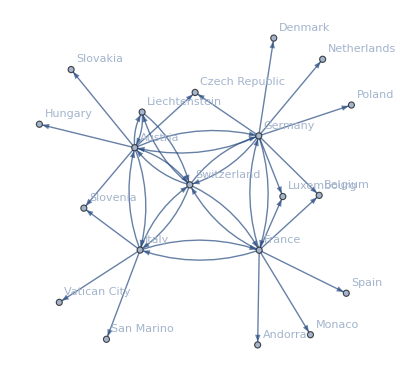

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],2,VertexLabels->All]
```

```mathematica
NestList[4#(1-#)&,0.2,100]
```

```mathematica
Nest[1+1/#&,1.,100]
```

1.61803

```mathematica
Nest[Sqrt[1+#]&,#,10]&/@Range[10]//N
```

{1.61803,1.61804,1.61804,1.61805,1.61805,1.61806,1.61806,1.61806,1.61807,1.61807}

```mathematica
Select[WordList[],#[[1]]=="p"&&#[[-1]]=="p"&]
```

{}

```mathematica
MatchQ[{a,x,b},{a,_,b}]
```

True

```mathematica
Cases[IntegerDigits[Range[10000]],{1,__,9}]
```

Part::partd: Part specification sda⟦1⟧ is longer than depth of object.

```mathematica
Select[IntegerDigits[2^1000],#==0||#==1&]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Cases[IntegerDigits[2^1000],0|1]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Select[IntegerDigits[Range[100,999]],First[#]==Last[#]&]
```

```mathematica
Cases[IntegerDigits[Range[100,999]],{x_,__,x_}]
```

```mathematica
Select[#>4&][{1,2.2,3,4.5,5,6,7.5,8}]
Select[#,#>4&]&[{1,2.2,3,4.5,5,6,7.5,8}]
```

{4.5,5,6,7.5,8}

{4.5,5,6,7.5,8}

{4.5,5,6,7.5,8}

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

```mathematica
f@@#&/@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

```mathematica
{x,x+1,x+2,x^2}/.x:>RandomInteger[100]
```

{16,91,27,8100}

```mathematica
{x,x+1,x+2,x^2}/.x->RandomInteger[100]
```

{32,33,34,1024}

```mathematica
Fib[1|2] = 1;Fib[n_Integer] := Fib[n-1] +Fib[n-2]
```

```mathematica
Fib/@Range[10]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
Clear[Fib]
```

```mathematica
ArrayPlot[CellularAutomaton[30, {{1}, 0}, 200]]
```

-Graphics-